## Variables and help functions

```mathematica
numberOfAgents = 100;
donationCost = -10;
buyCost = -40;
donationHealthChange=7;
usageUtil = 5;
waitCost = -1;
fullToolHealth=10;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
0.5,
RandomReal[], (* Prob to buy tool *)
RandomReal[], (* Prob to donate *)
0, (* Has tool (tool health) *)
0 (* payoff *)
}],numberOfAgents];
```

Calculate payoff now has a max number of tools so that a player that donates doesn’t have to if the pool is full.

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_,maxPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=agent[[5]],poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util+=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=fullToolHealth;
util+=buyCost+usageUtil,
If[nPTools>0,
util+=usageUtil;poolHealthChange-=1,
util+=waitCost]
]
],
If[RandomReal[]<pd &&nPTools<=maxPTools,
poolHealthChange+=donationHealthChange;
util+=donationCost,
util+=0
]
];
{{p,pb,pd,toolHealth,util},poolHealthChange}
];

CalculatePayoff[{0,0,1,5,0},3,4]
```

{{0,0,1,5,-10},7}

```mathematica
MutateValue[v_] := Module[{value},
If[v>0.5,distance = 1-v,distance =v];
value=RandomVariate[NormalDistribution[v,(*distance/4)+*)0.1]];
If[value<=0,0,Min[value,1]]
];
MutateValue[0.1]
MutateAgent[agent_]:=Module[
{p=agent[[1]],pb=agent[[2]],pd=agent[[3]],a4=agent[[4]],a5=agent[[5]]},
{p,MutateValue[pb],MutateValue[pd],a4,a5}
];
```

0.161778

## dorounds

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {},
maxPoolTools=Length[agentList]*1.2},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullToolHealth;
(*agents=RandomSample[agents];*)
agents=Sort[agents,#1[[3]]>#2[[3]]&];
For[j=1,j≤Length[agents],j++,
{newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools,maxPoolTools];
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools=poolHealth/fullToolHealth;
];

PHhistory = Append[PHhistory,poolHealth];
];
{agents, PHhistory}
];
```

## Simulation with pool resetting

Simulation clears pool health after each round. This means that mutated agents start with a new pool.

```mathematica
RunSim[agentList_]:=Module[{agents=agentList,history={},avgPHist={}},
For[k=1,k<100,k++,
{ag, ph} =DoRound[agents,30,100];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/4];
newAgents=Join[newAgents,newAgents,newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.1,MutateAgent[a],a]],newAgents];
agents=newAgents;
avgP=N[Total[Map[Function[x,Last[x]],ag]]/Length[ag]];
avgPHist=Append[avgPHist,avgP];
history=Append[history, ph];
];
{ag, ph} =DoRound[agents,30,100];
avgP=N[Total[Map[Function[x,Last[x]],ag]]/Length[ag]];
avgPHist=Append[avgPHist,avgP];
history=Append[history, ph];
{ag, history,avgPHist}
];
```

### results

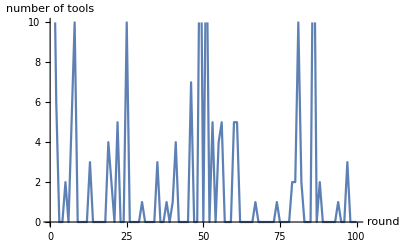

39.53

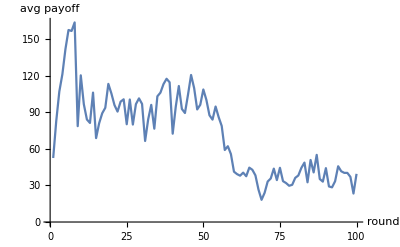

{{0.5,0.123974,0,0,93},{0.5,0,0.0533286,0,90},{0.5,0,0.0533286,0,88},{0.5,0,0.0571344,0,87},{0.5,0,0.0571344,0,83},{0.5,0,0.036481,0,82},{0.5,0,0.0571344,0,82},{0.5,0,0.0533286,0,76},{0.5,0,0.036481,0,75},{0.5,0,0.036481,0,75},{0.5,0,0.0571344,0,74},{0.5,0.108782,0,0,70},{0.5,0,0.0533286,0,69},{0.5,0,0.0571344,0,69},{0.5,0,0.0129782,0,65},{0.5,0,0.0533286,0,65},{0.5,0.049812,0.042822,0,64},{0.5,0,0.036481,0,62},{0.5,0,0.0571344,0,62},{0.5,0,0.0571344,0,61},{0.5,0,0.0571344,0,60},{0.5,0,0.0571344,0,59},{0.5,0,0.0571344,0,58},{0.5,0,0.0571344,0,57},{0.5,0,0.0129782,0,56},{0.5,0,0.0571344,0,56},{0.5,0,0.0571344,0,56},{0.5,0.049812,0.042822,7,54},{0.5,0,0.0571344,0,54},{0.5,0,0.0571344,0,54},{0.5,0,0.0533286,0,52},{0.5,0,0.0571344,0,52},{0.5,0,0.0571344,0,51},{0.5,0.049812,0.042822,0,50},{0.5,0,0.036481,0,49},{0.5,0,0.0533286,0,49},{0.5,0,0.0571344,0,49},{0.5,0,0.0571344,0,46},{0.5,0,0.0533286,0,45},{0.5,0,0.0533286,0,43},{0.5,0,0.0571344,0,43},{0.5,0,0.0571344,0,43},{0.5,0,0.0571344,0,43},{0.5,0,0.036481,0,42},{0.5,0,0.036481,0,42},{0.5,0,0.0533286,0,42},{0.5,0,0.0533286,0,42},{0.5,0,0.0533286,0,41},{0.5,0,0.0571344,0,41},{0.5,0,0.0571344,0,40},{0.5,0,0.036481,0,39},{0.5,0,0.0571344,0,39},{0.5,0,0.0571344,0,39},{0.5,0,0.0533286,0,38},{0.5,0,0.0533286,0,38},{0.5,0,0.0571344,0,37},{0.5,0,0.0129782,0,36},{0.5,0,0.0533286,0,36},{0.5,0,0.0571344,0,36},{0.5,0,0.0571344,0,35},{0.5,0,0.0533286,0,34},{0.5,0,0.0210937,0,31},{0.5,0,0.031772,0,31},{0.5,0,0.0571344,0,31},{0.5,0,0.036481,0,30},{0.5,0,0.036481,0,30},{0.5,0,0.0571344,0,29},{0.5,0,0.0533286,0,28},{0.5,0,0.0571344,0,27},{0.5,0,0.0571344,0,27},{0.5,0,0.036481,0,26},{0.5,0,0.0571344,0,26},{0.5,0,0.036481,0,25},{0.5,0,0.0413737,0,25},{0.5,0,0.0533286,0,24},{0.5,0,0.0571344,0,24},{0.5,0,0.0571344,0,24},{0.5,0,0.036481,0,23},{0.5,0,0.036481,0,22},{0.5,0,0.0533286,0,21},{0.5,0,0.0533286,0,21},{0.5,0,0.0571344,0,21},{0.5,0,0.036481,0,20},{0.5,0,0.0533286,0,20},{0.5,0,0.0571344,0,20},{0.5,0,0.0533286,0,18},{0.5,0,0.0571344,0,16},{0.5,0,0.0571344,0,16},{0.5,0,0.0571344,0,15},{0.5,0,0.0571344,0,14},{0.5,0,0.0571344,0,13},{0.5,0,0.0571344,0,13},{0.5,0.049812,0.042822,0,5},{0.5,0,0.0571344,0,1},{0.5,0,0.036481,0,-1},{0.5,0,0.0571344,0,-1},{0.5,0,0.0778842,0,-11},{0.5,0,0.0571344,0,-22},{0.5,0,0.0571344,0,-48},{0.5,0,0.163191,0,-49}}

{0.5,0.00432004,0.0504491,7/100,3953/100}

```mathematica
{a,h,p}=RunSim[agentParams];
ListLinePlot[h[[-1]],AxesLabel->{"round", "number of tools"}]
N[Total[Map[Function[x,Last[x]],a]]/Length[a]] (*average payoff*)
ListLinePlot[p,AxesLabel->{"round", "avg payoff"}]
Sort[a,Last[#1]>Last[#2]&]
Mean[a]
```

We see that we get a mixed stable equilibrium where everyone donates a bit. Below we plot the evolution of pool health over the generations.

```mathematica
hh={};
For[i=1,i≤Length[h],i++,
For[j=1,j≤Length[h[[i]]],j++,
hh=Append[hh,{i,j,h[[i]][[j]]}];
]
];
ListPlot3D[hh, AxesLabel->{evolutionNr,round,poolHealth}]
```

-Graphics3D-

## Simulation for not resetting tool usage

Simulation runs with agents mutating while pool is still functioning. Now if a lot of people donated in the past a new mutation can take advantage of this and vice versa.

```mathematica
RunSimContinuous[agentList_,initHealth_]:=Module[{agents=agentList,history={},avgPHist={},poolHealth=initHealth},
For[k=1,k<100,k++,
{ag, ph} =DoRound[agents,poolHealth,100];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/4];
newAgents=Join[newAgents,newAgents,newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
avgP=N[Total[Map[Function[x,Last[x]],ag]]/Length[ag]];
avgPHist=Append[avgPHist,avgP];
history=Join[history, ph];
poolHealth=ph[[-1]];
];
{ag, ph} =DoRound[agents,poolHealth,100];
avgP=N[Total[Map[Function[x,Last[x]],ag]]/Length[ag]];
avgPHist=Append[avgPHist,avgP];
history=Join[history, ph];
{ag, history,avgPHist}
];
```

### Results

Run the model with 80 initial tools. We see a drop off after 500 rounds. This is probably because some agents realize that they can defect and be better of than anyone else. Or that they realize that they don’t have to buy tools and can just use the pool. Meaning that the pool runs out of tools. We also plot the average payoff for each round.

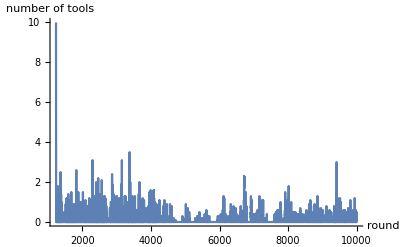

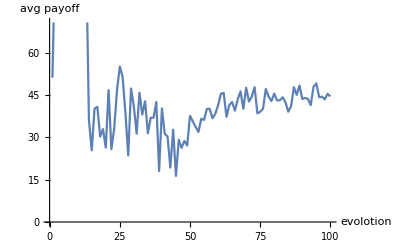

{{0.5,0.527542,0,0,85},{0.5,0.545853,0,2,74},{0.5,0.545853,0,0,73},{0.5,0.545853,0,0,71},{0.5,0.545853,0,2,71},{0.5,0.527542,0,1,69},{0.5,0.419054,0,0,69},{0.5,0.545853,0,4,68},{0.5,0.419054,0,0,67},{0.5,0.472911,0,1,67},{0.5,0.419054,0,1,67},{0.5,0.527542,0,3,64},{0.5,0.358652,0,0,62},{0.5,0.545853,0,0,62},{0.5,0.545853,0,0,62},{0.5,0.358652,0,1,61},{0.5,0.545853,0,0,60},{0.5,0.527542,0,3,59},{0.5,0.545853,0,2,59},{0.5,0.419054,0,0,59},{0.5,0.527542,0,1,59},{0.5,0.545853,0,7,59},{0.5,0.419054,0,0,56},{0.5,0.419054,0,0,56},{0.5,0.419054,0,0,55},{0.5,0.527542,0,1,55},{0.5,0.545853,0,4,55},{0.5,0.527542,0,1,54},{0.5,0.527542,0,0,54},{0.5,0.419054,0,4,54},{0.5,0.545853,0,1,53},{0.5,0.527542,0,5,53},{0.5,0.545853,0,1,53},{0.5,0.527542,0,0,53},{0.5,0.419054,0,1,52},{0.5,0.545853,0,5,52},{0.5,0.545853,0,6,49},{0.5,0.419054,0,1,49},{0.5,0.472911,0,7,48},{0.5,0.545853,0,2,47},{0.5,0.545853,0,8,47},{0.5,0.419054,0,2,47},{0.5,0.527542,0,1,47},{0.5,0.545853,0,2,47},{0.5,0.545853,0,3,47},{0.5,0.527542,0,6,47},{0.5,0.472911,0,7,45},{0.5,0.545853,0,8,45},{0.5,0.472911,0,2,44},{0.5,0.545853,0,7,44},{0.5,0.527542,0,7,44},{0.5,0.527542,0,3,44},{0.5,0.545853,0,10,44},{0.5,0.545853,0,6,43},{0.5,0.527542,0,8,43},{0.5,0.545853,0,6,43},{0.5,0.472911,0,4,43},{0.5,0.419054,0,6,42},{0.5,0.419054,0,3,41},{0.5,0.419054,0,5,40},{0.5,0.419054,0,8,40},{0.5,0.527542,0,7,40},{0.5,0.527542,0,9,39},{0.5,0.523311,0,8,39},{0.5,0.527542,0,5,39},{0.5,0.419054,0,6,39},{0.5,0.545853,0,5,39},{0.5,0.358652,0,8,38},{0.5,0.419054,0,9,37},{0.5,0.527542,0,8,37},{0.5,0.545853,0,8,36},{0.5,0.527542,0,4,36},{0.5,0.419054,0,9,35},{0.5,0.527542,0,5,35},{0.5,0.419054,0,9,34},{0.5,0.545853,0,9,33},{0.5,0.358652,0,4,32},{0.5,0.527542,0,6,32},{0.5,0.419054,0,7,32},{0.5,0.472911,0,9,31},{0.5,0.472911,0,9,31},{0.5,0.358652,0,8,31},{0.5,0.358652,0,9,31},{0.5,0.591283,0.127935,0,30},{0.5,0.545853,0,9,28},{0.5,0.339069,0,9,28},{0.5,0.479492,0,7,27},{0.5,0.419054,0,8,27},{0.5,0.545853,0,9,27},{0.5,0.527542,0,10,25},{0.5,0.527542,0,10,25},{0.5,0.527542,0,10,25},{0.5,0.419054,0,10,24},{0.5,0.545853,0,9,24},{0.5,0.358652,0,5,23},{0.5,0.527542,0,10,18},{0.5,0.419054,0,10,14},{0.5,0.47638,0.0769255,4,14},{0.5,0.358652,0,7,13},{0.5,0.667266,0.0766353,5,-22}}

{0.5,0.489863,0.00281496,118/25,1112/25}

```mathematica
{a,h,p}=RunSimContinuous[agentParams,20];
ListLinePlot[Map[Function[x, x/fullToolHealth],h],AxesLabel->{"round", "number of tools"},PlotRange->{5,5}](* plot the number of tools in the pool at any given time *)
ListLinePlot[p,AxesLabel->{"evolotion", "avg payoff"}]
Sort[a,Last[#1]>Last[#2]&]
Mean[a]
```

We try the same thing but with fewer initial tools. This does not change much and a mixed strategy equilibrium can be observed here as well.

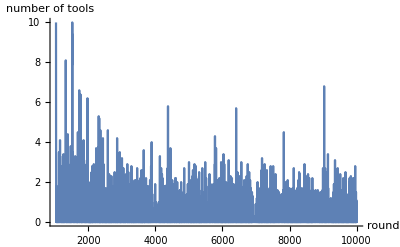

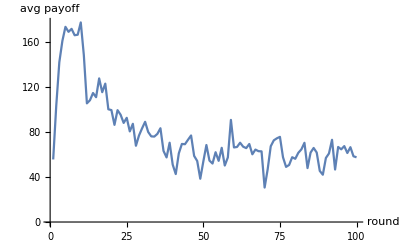

{{0.5,0,0.0565748,0,137},{0.5,0,0.0751701,0,119},{0.5,0,0.0751701,0,103},{0.5,0,0.0751701,0,101},{0.5,0,0.0751701,0,100},{0.5,0,0.0565748,0,95},{0.5,0,0.0751701,0,93},{0.5,0,0.0751701,0,92},{0.5,0,0.0751701,0,91},{0.5,0,0.0565748,0,90},{0.5,0,0.0565748,0,90},{0.5,0,0.0751701,0,90},{0.5,0,0.0751701,0,88},{0.5,0,0.0565748,0,87},{0.5,0,0.0565748,0,85},{0.5,0,0.0565748,0,84},{0.5,0,0.0565748,0,83},{0.5,0,0.0751701,0,83},{0.5,0,0,0,80},{0.5,0,0.0751701,0,80},{0.5,0,0.0751701,0,80},{0.5,0,0,0,79},{0.5,0,0.0751701,0,78},{0.5,0,0.0751701,0,78},{0.5,0,0.0751701,0,76},{0.5,0,0.0565748,0,75},{0.5,0,0.0565748,0,75},{0.5,0,0.0751701,0,74},{0.5,0,0.0751701,0,74},{0.5,0,0.0751701,0,73},{0.5,0,0.0751701,0,72},{0.5,0,0.0751701,0,71},{0.5,0,0,0,70},{0.5,0,0.0751701,0,70},{0.5,0,0.0751701,0,70},{0.5,0,0.0751701,0,69},{0.5,0,0.0751701,0,66},{0.5,0,0.0751701,0,66},{0.5,0,0,0,65},{0.5,0,0.0565748,0,65},{0.5,0,0.0751701,0,65},{0.5,0,0.0751701,0,65},{0.5,0,0.0751701,0,65},{0.5,0,0,0,64},{0.5,0,0.0565748,0,64},{0.5,0,0.0565748,0,63},{0.5,0,0.0565748,0,62},{0.5,0,0.0751701,0,61},{0.5,0,0.0751701,0,61},{0.5,0,0.0751701,0,61},{0.5,0,0.0751701,0,61},{0.5,0,0.0565748,0,60},{0.5,0.0168298,0.00501517,2,59},{0.5,0,0.0751701,0,59},{0.5,0,0.0751701,0,59},{0.5,0,0.0751701,0,59},{0.5,0,0,0,58},{0.5,0,0.0565748,0,56},{0.5,0,0.0565748,0,55},{0.5,0,0.0751701,0,55},{0.5,0,0.0751701,0,54},{0.5,0,0.0751701,0,53},{0.5,0,0.0751701,0,53},{0.5,0,0.0751701,0,53},{0.5,0,0.0751701,0,52},{0.5,0,0.0751701,0,52},{0.5,0,0.0751701,0,52},{0.5,0,0.0751701,0,50},{0.5,0.0330728,0.0797635,0,49},{0.5,0,0.0751701,0,46},{0.5,0,0.0751701,0,45},{0.5,0,0.0751701,0,45},{0.5,0,0.0751701,0,45},{0.5,0,0.0751701,0,45},{0.5,0,0.0565748,0,44},{0.5,0,0.0751701,0,44},{0.5,0,0.0751701,0,44},{0.5,0,0.0751701,0,44},{0.5,0,0.0751701,0,42},{0.5,0,0.0565748,0,39},{0.5,0,0.0751701,0,38},{0.5,0,0.0751701,0,37},{0.5,0,0.0751701,0,35},{0.5,0,0.0751701,0,31},{0.5,0,0.0751701,0,29},{0.5,0,0.0751701,0,29},{0.5,0,0.0751701,0,25},{0.5,0,0.0751701,0,24},{0.5,0,0.0751701,0,23},{0.5,0,0.0751701,0,23},{0.5,0,0.0751701,0,18},{0.5,0,0.0751701,0,14},{0.5,0,0.0751701,0,7},{0.5,0,0.0751701,0,0},{0.5,0,0.0565748,0,-1},{0.5,0,0.0751701,0,-4},{0.5,0,0.0751701,0,-10},{0.5,0,0.168919,0,-12},{0.5,0,0.0751701,0,-20},{0.5,0,0.0751701,0,-26}}

{0.5,0.000499026,0.0672227,1/50,287/5}

```mathematica
{a,h,p}=RunSimContinuous[agentParams,20];
ListLinePlot[Map[Function[x, x/fullToolHealth],h],AxesLabel->{"round", "number of tools"},PlotRange->{5,5}](* plot the number of tools in the pool at any given time *)
ListLinePlot[p,AxesLabel->{"evolution", "avg payoff"}]
Sort[a,Last[#1]>Last[#2]&]
Mean[a]
```